## Chapter 21 Numerics For ODEs and PDEs

## 21.1 Euler Method::

```mathematica
Clear[f,x,y]
```

```mathematica
f[x_,y_] =-5x^4 y^2
```

-5 x^4 y^2

```mathematica
h =0.2;M=10;x[0]=0;y[0]=1;
```

```mathematica
Do[y[n+1]=N[y[n]+h f[x[n],y[n]]];
x[n+1]=N[x[n]+h],{n,0,M}]
```

```mathematica
Table[{x[n],y[n],1/(1+x[n]^5)-y[n]},{n,0,M}]
```

{{0,1,0},{0.2,1.,-0.000319898},{0.4,0.9984,-0.00853621},{0.6,0.972882,-0.0450315},{0.8,0.850216,-0.097022},{1.,0.554129,-0.0541294},{1.2,0.24707,0.0396009},{1.4,0.12049,0.036293},{1.6,0.0647183,0.0223461},{1.8,0.0372688,0.0129934},{2.,0.022688,0.00761501}}

```mathematica
p1 =ListPlot[Table[{x[n],y[n]},{n,0,M}],Prolog->AbsolutePointSize[4]]
```

-Graphics-

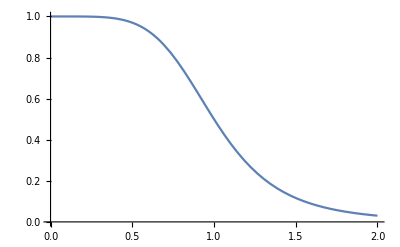

```mathematica
P2=Plot[1 /(1+x^5),{x,0,2}]
```

```mathematica
Show[p1,P2]
```

-Graphics-

## 21.2 Improved Euler Method::

```mathematica
f[x_,y_]=1+y^2
```

1+y^2

```mathematica
Clear[h,M,x,y]
```

```mathematica
h=0.1;M=10;x[0]=0;y[0]=0;
```

```mathematica
Do [
yatar=y[n]+h f[x[n],y[n]];
y[n+1]=y[n]+h /2 (f[x[n],y[n]]+f[x[n]+h,yatar]);
x[n+1]=x[n]+h,{n,0,M}
]
```

```mathematica
Table[{x[n],y[n],Tan[x[n]]-y[n]},{n,0,M}]
```

{{0,0,0},{0.1,0.1005,-0.000165328},{0.2,0.203035,-0.000325292},{0.3,0.309814,-0.000477536},{0.4,0.423408,-0.000615128},{0.5,0.547024,-0.000721811},{0.6,0.684899,-0.000762192},{0.7,0.842949,-0.000660151},{0.8,1.02989,-0.000248368},{0.9,1.2593,0.00085887},{1.,1.55379,0.00361822}}

```mathematica
P11 =ListPlot[Table[{x[n],y[n]},{n,0,M}],Prolog->AbsolutePointSize[4]]
```

-Graphics-

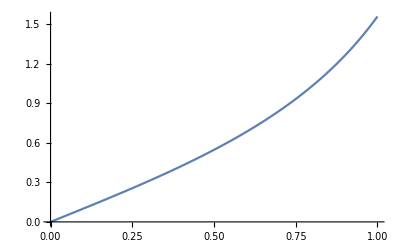

```mathematica
P22=Plot[Tan[x],{x,0,1}]
```

```mathematica
Show[P11,P22]
```

-Graphics-

## 21.3 Classical Runge -Kutta Method (RK),Module::

```mathematica
RK[f_,x_,y_,h_,M_]
```

RK[f_,x_,y_,h_,M_]

```mathematica
Module[{n},
Do[
k1 =hf[x[n],y[n]];k2=hf[x[n]+h/2,y[n]+k1/2];
k3=hf[x[n]+h/2,y[n]+k2/2];
k4=hf[x[n]+h,y[n]+k3];
y[n+1]=y[n]+1/6(k1+2k2+2k3+k4); x[n+1]=x[n]+h,{n,0,M}]
]
```

```mathematica
DeleteFile["RK.m"]
```

```mathematica
Clear[f,x,y,h,M]
```

```mathematica
Save["RK.m",RK]
```

```mathematica
||RK.m
```

```mathematica
f[x_,y_]=1+y^2;
```

```mathematica
x[0]=0;y[0]=0;h=0.1;M=10;
```

```mathematica
RK[f,x,y,h,K]
```

RK[f,x,y,0.1,K]

```mathematica
Table[{x[n],y[n],Tan[x[n]]-y[n]},{n,0,10}]
```

{{0,0,0},{x[1],y[1],Tan[x[1]]-y[1]},{x[2],y[2],Tan[x[2]]-y[2]},{x[3],y[3],Tan[x[3]]-y[3]},{x[4],y[4],Tan[x[4]]-y[4]},{x[5],y[5],Tan[x[5]]-y[5]},{x[6],y[6],Tan[x[6]]-y[6]},{x[7],y[7],Tan[x[7]]-y[7]},{x[8],y[8],Tan[x[8]]-y[8]},{x[9],y[9],Tan[x[9]]-y[9]},{x[10],y[10],Tan[x[10]]-y[10]}}

## 21.4 Adams-Moulton Multistep Method::

```mathematica
<<RK.m
```

```mathematica
AdamsMoultonRK[f_,x_,y_,h_,M_]:= Module[{n,ystar},
Do[
k1 =hf[x[n],y[n]];
k2 =hf[x[n]+h/2,y[n]+k1/2];
k3=hf[x[n]+h/2,y[n]+k2/2];
k4=hf[x[n]+h,y[n]+k3];
y[n+1]=y[n]+1/6(k1+2k2+2k3+k4);
x[n+1]=x[n]+h,{n,0,3}]];
```

```mathematica
Do[
x[n+1]=x[n]+h;
ystar =y[n]+h/24(55f[x[n],y[n]]-59f[x[n-1],y[n-1]]+37f[x[n-2],y[n-2]]-9f[x[n-3],y[n-3]]);
y[n+1]=y[n]+h/24(9f[x[n+1],ystar]+ 19f[x[n],y[n]]-5f[x[n-1],y[n-1]]+f[x[n-2],y[n-2]]),{n,3,M}]
```

```mathematica
f[x_,y_,yp_]=xy
```

xy

```mathematica
x[0]=0;y[0]=0.355028;yp[0]=-0.28809;h=0.2;M=5;
```

```mathematica
RNK[f,x,yp,h,M]
```

RNK[f,x,yp,0.2,5]

```mathematica
Table[{x[n],y[n],yp[n]},{n,0,M}]
```

{{0,0.355028,-0.28809},{x[1],y[1],yp[1]},{x[2],y[2],yp[2]},{x[3],y[3],yp[3]},{0.1+x[3],y[3]+0.00416667 (1+y[1]^2-5 (1+y[2]^2)+19 (1+y[3]^2)+9 (1+(y[3]+0.00416667 (-9+37 (1+y[1]^2)-59 (1+y[2]^2)+55 (1+y[3]^2)))^2)),yp[4]},{0.2+x[3],y[3]+0.00416667 (1+y[1]^2-5 (1+y[2]^2)+19 (1+y[3]^2)+9 (1+(y[3]+0.00416667 (-9+37 (1+y[1]^2)-59 (1+y[2]^2)+55 (1+y[3]^2)))^2))+0.00416667 (1+y[2]^2-5 (1+y[3]^2)+19 (1+(y[3]+0.00416667 (1+y[1]^2-5 (1+y[2]^2)+19 (1+y[3]^2)+9 (1+(y[3]+0.00416667 (-9+37 (1+y[1]^2)-59 (1+y[2]^2)+55 (1+y[3]^2)))^2)))^2)+9 (1+(y[3]+0.00416667 (1+y[1]^2-5 (1+y[2]^2)+19 (1+y[3]^2)+9 (1+(y[3]+0.00416667 (-9+37 (1+y[1]^2)-59 (1+y[2]^2)+55 (1+y[3]^2)))^2))+0.00416667 (-9 (1+y[1]^2)+37 (1+y[2]^2)-59 (1+y[3]^2)+55 (1+(y[3]+0.00416667 (1+y[1]^2-5 (1+y[2]^2)+19 (1+y[3]^2)+9 (1+(y[3]+0.00416667 (-9+37 (1+y[1]^2)-59 (1+y[2]^2)+55 (1+y[3]^2)))^2)))^2)))^2)),yp[5]}}

## 21.7 Laplace Equation.Boundary Value Problem::

```mathematica
A ={{-4,1,1,0},{1,-4,0,1},{1,0,-4,1},{0,1,1,-4}}
```

{{-4,1,1,0},{1,-4,0,1},{1,0,-4,1},{0,1,1,-4}}

```mathematica
%//MatrixForm
```

(-4 | 1 | 1 | 0
1 | -4 | 0 | 1
1 | 0 | -4 | 1
0 | 1 | 1 | -4)

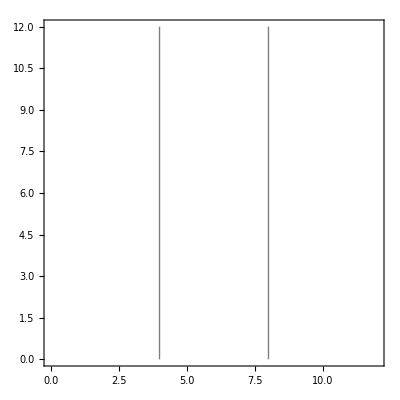

```mathematica
P1 =ContourPlot[x,{x,0,12},{y,0,12},Contours->2,ContourShading->False]
```

```mathematica
c ={100,100,100,100,0,0,100,100};
```

```mathematica
B =ZeroMatrix[4,8]
```

```mathematica
ZeroMatrix[4,8]
```

ZeroMatrix[4,8]

## 21.8 Heat EQuation ,Crank- Nicolson Method::

```mathematica
p2 = ContourPlot[y,{x,0,12};{y,0,12},Contours-> 2, ContourShading-> False]
```

ContourPlot::pllim: Range specification {x,0,12};{y,0,12} is not of the form {x, xmin, xmax}.

General::stop: Further output of ContourPlot::pllim will be suppressed during this calculation.

```mathematica
n=4;r=1;h=0.2;
```

```mathematica
A1 =Table[Switch[j-k,0,4,1,-1,-1,-1,_,0],{j,n},{k,n}];
```

```mathematica
MatrixForm[A1]
```

(4 | -1 | 0 | 0
-1 | 4 | -1 | 0
0 | -1 | 4 | -1
0 | 0 | -1 | 4)

```mathematica
n=4;
```

```mathematica
Clear[u]
```

```mathematica
Do[u[k],{k,0,n+1}]
```

```mathematica
Table[Temp[k],{k,1,n+1}];
```

```mathematica
M=5;
```

```mathematica
Do[b =Table[0,{i,1,n}];
Do[b[[k]]=u[k-1]+u[k+1],{k,1,n}];
v=N[LinearSolve[A,b]];
Print[v];Temp[j]=v;
Do[u[k]=v[[k]],{k,1,n}],{j,1,M}];
```

{0.0416667 (-7. u[0.]-2. u[1.]-9. u[2.]-3. u[3.]-2. u[4.]-1. u[5.]),0.0416667 (-2. u[0.]-7. u[1.]-3. u[2.]-9. u[3.]-1. u[4.]-2. u[5.]),0.0416667 (-2. u[0.]-1. u[1.]-9. u[2.]-3. u[3.]-7. u[4.]-2. u[5.]),0.0416667 (-1. u[0.]-2. u[1.]-3. u[2.]-9. u[3.]-2. u[4.]-7. u[5.])}

{-1. (0.222222 u[0.]-0.128472 u[1.]-0.135417 u[2.]-0.197917 u[3.]-0.0659722 u[4.]-0.0277778 u[5.]),-1. (-0.0451389 u[0.]-0.0798611 u[1.]-0.270833 u[2.]-0.145833 u[3.]-0.142361 u[4.]+0.0173611 u[5.]),-1. (0.0173611 u[0.]-0.142361 u[1.]-0.145833 u[2.]-0.270833 u[3.]-0.0798611 u[4.]-0.0451389 u[5.]),-1. (-0.0277778 u[0.]-0.0659722 u[1.]-0.197917 u[2.]-0.135417 u[3.]-0.128472 u[4.]+0.222222 u[5.])}

{-1. (0.29022 u[0.]+0.0639468 u[1.]+0.147569 u[2.]+0.116319 u[3.]+0.0795718 u[4.]+0.0245949 u[5.]),-1. (0.0188079 u[0.]+0.103588 u[1.]+0.136285 u[2.]+0.18316 u[3.]+0.072338 u[4.]+0.0969329 u[5.]),-1. (0.0969329 u[0.]+0.072338 u[1.]+0.18316 u[2.]+0.136285 u[3.]+0.103588 u[4.]+0.0188079 u[5.]),-1. (0.0245949 u[0.]+0.0795718 u[1.]+0.116319 u[2.]+0.147569 u[3.]+0.0639468 u[4.]+0.29022 u[5.])}

{-1. (0.246263 u[0.]-0.0598476 u[1.]-0.0959925 u[2.]-0.107711 u[3.]-0.0520351 u[4.]-0.0232687 u[5.]),-1. (-0.0410397 u[0.]-0.0620419 u[1.]-0.133608 u[2.]-0.114077 u[3.]-0.0737606 u[4.]+0.0448978 u[5.]),-1. (0.0448978 u[0.]-0.0737606 u[1.]-0.114077 u[2.]-0.133608 u[3.]-0.0620419 u[4.]-0.0410397 u[5.]),-1. (-0.0232687 u[0.]-0.0520351 u[1.]-0.107711 u[2.]-0.0959925 u[3.]-0.0598476 u[4.]+0.246263 u[5.])}

{-1. (0.282862 u[0.]+0.0418093 u[1.]+0.081338 u[2.]+0.0764552 u[3.]+0.044739 u[4.]+0.0113772 u[5.]),-1. (0.000769596 u[0.]+0.0550391 u[1.]+0.0919657 u[2.]+0.0997782 u[3.]+0.0501563 u[4.]+0.0896368 u[5.]),-1. (0.0896368 u[0.]+0.0501563 u[1.]+0.0997782 u[2.]+0.0919657 u[3.]+0.0550391 u[4.]+0.000769596 u[5.]),-1. (0.0113772 u[0.]+0.044739 u[1.]+0.0764552 u[2.]+0.081338 u[3.]+0.0418093 u[4.]+0.282862 u[5.])}

```mathematica
V =Table[Table[Temp[k][[j]],{j,1,M-1}],{k,1,n+1}]
```

{{0.0416667 (-7. u[0.]-2. u[1.]-9. u[2.]-3. u[3.]-2. u[4.]-1. u[5.]),0.0416667 (-2. u[0.]-7. u[1.]-3. u[2.]-9. u[3.]-1. u[4.]-2. u[5.]),0.0416667 (-2. u[0.]-1. u[1.]-9. u[2.]-3. u[3.]-7. u[4.]-2. u[5.]),0.0416667 (-1. u[0.]-2. u[1.]-3. u[2.]-9. u[3.]-2. u[4.]-7. u[5.])},{-1. (0.222222 u[0.]-0.128472 u[1.]-0.135417 u[2.]-0.197917 u[3.]-0.0659722 u[4.]-0.0277778 u[5.]),-1. (-0.0451389 u[0.]-0.0798611 u[1.]-0.270833 u[2.]-0.145833 u[3.]-0.142361 u[4.]+0.0173611 u[5.]),-1. (0.0173611 u[0.]-0.142361 u[1.]-0.145833 u[2.]-0.270833 u[3.]-0.0798611 u[4.]-0.0451389 u[5.]),-1. (-0.0277778 u[0.]-0.0659722 u[1.]-0.197917 u[2.]-0.135417 u[3.]-0.128472 u[4.]+0.222222 u[5.])},{-1. (0.29022 u[0.]+0.0639468 u[1.]+0.147569 u[2.]+0.116319 u[3.]+0.0795718 u[4.]+0.0245949 u[5.]),-1. (0.0188079 u[0.]+0.103588 u[1.]+0.136285 u[2.]+0.18316 u[3.]+0.072338 u[4.]+0.0969329 u[5.]),-1. (0.0969329 u[0.]+0.072338 u[1.]+0.18316 u[2.]+0.136285 u[3.]+0.103588 u[4.]+0.0188079 u[5.]),-1. (0.0245949 u[0.]+0.0795718 u[1.]+0.116319 u[2.]+0.147569 u[3.]+0.0639468 u[4.]+0.29022 u[5.])},{-1. (0.246263 u[0.]-0.0598476 u[1.]-0.0959925 u[2.]-0.107711 u[3.]-0.0520351 u[4.]-0.0232687 u[5.]),-1. (-0.0410397 u[0.]-0.0620419 u[1.]-0.133608 u[2.]-0.114077 u[3.]-0.0737606 u[4.]+0.0448978 u[5.]),-1. (0.0448978 u[0.]-0.0737606 u[1.]-0.114077 u[2.]-0.133608 u[3.]-0.0620419 u[4.]-0.0410397 u[5.]),-1. (-0.0232687 u[0.]-0.0520351 u[1.]-0.107711 u[2.]-0.0959925 u[3.]-0.0598476 u[4.]+0.246263 u[5.])},{-1. (0.282862 u[0.]+0.0418093 u[1.]+0.081338 u[2.]+0.0764552 u[3.]+0.044739 u[4.]+0.0113772 u[5.]),-1. (0.000769596 u[0.]+0.0550391 u[1.]+0.0919657 u[2.]+0.0997782 u[3.]+0.0501563 u[4.]+0.0896368 u[5.]),-1. (0.0896368 u[0.]+0.0501563 u[1.]+0.0997782 u[2.]+0.0919657 u[3.]+0.0550391 u[4.]+0.000769596 u[5.]),-1. (0.0113772 u[0.]+0.044739 u[1.]+0.0764552 u[2.]+0.081338 u[3.]+0.0418093 u[4.]+0.282862 u[5.])}}

```mathematica
V[[3]]
```

{-1. (0.29022 u[0.]+0.0639468 u[1.]+0.147569 u[2.]+0.116319 u[3.]+0.0795718 u[4.]+0.0245949 u[5.]),-1. (0.0188079 u[0.]+0.103588 u[1.]+0.136285 u[2.]+0.18316 u[3.]+0.072338 u[4.]+0.0969329 u[5.]),-1. (0.0969329 u[0.]+0.072338 u[1.]+0.18316 u[2.]+0.136285 u[3.]+0.103588 u[4.]+0.0188079 u[5.]),-1. (0.0245949 u[0.]+0.0795718 u[1.]+0.116319 u[2.]+0.147569 u[3.]+0.0639468 u[4.]+0.29022 u[5.])}

```mathematica
V[[3,2]]
```

-1. (0.0188079 u[0.]+0.103588 u[1.]+0.136285 u[2.]+0.18316 u[3.]+0.072338 u[4.]+0.0969329 u[5.])

```mathematica
W =Table[Join[{0},V[[j]],{0}],{j,1,M}]
```

{{0,0.0416667 (-7. u[0.]-2. u[1.]-9. u[2.]-3. u[3.]-2. u[4.]-1. u[5.]),0.0416667 (-2. u[0.]-7. u[1.]-3. u[2.]-9. u[3.]-1. u[4.]-2. u[5.]),0.0416667 (-2. u[0.]-1. u[1.]-9. u[2.]-3. u[3.]-7. u[4.]-2. u[5.]),0.0416667 (-1. u[0.]-2. u[1.]-3. u[2.]-9. u[3.]-2. u[4.]-7. u[5.]),0},{0,-1. (0.222222 u[0.]-0.128472 u[1.]-0.135417 u[2.]-0.197917 u[3.]-0.0659722 u[4.]-0.0277778 u[5.]),-1. (-0.0451389 u[0.]-0.0798611 u[1.]-0.270833 u[2.]-0.145833 u[3.]-0.142361 u[4.]+0.0173611 u[5.]),-1. (0.0173611 u[0.]-0.142361 u[1.]-0.145833 u[2.]-0.270833 u[3.]-0.0798611 u[4.]-0.0451389 u[5.]),-1. (-0.0277778 u[0.]-0.0659722 u[1.]-0.197917 u[2.]-0.135417 u[3.]-0.128472 u[4.]+0.222222 u[5.]),0},{0,-1. (0.29022 u[0.]+0.0639468 u[1.]+0.147569 u[2.]+0.116319 u[3.]+0.0795718 u[4.]+0.0245949 u[5.]),-1. (0.0188079 u[0.]+0.103588 u[1.]+0.136285 u[2.]+0.18316 u[3.]+0.072338 u[4.]+0.0969329 u[5.]),-1. (0.0969329 u[0.]+0.072338 u[1.]+0.18316 u[2.]+0.136285 u[3.]+0.103588 u[4.]+0.0188079 u[5.]),-1. (0.0245949 u[0.]+0.0795718 u[1.]+0.116319 u[2.]+0.147569 u[3.]+0.0639468 u[4.]+0.29022 u[5.]),0},{0,-1. (0.246263 u[0.]-0.0598476 u[1.]-0.0959925 u[2.]-0.107711 u[3.]-0.0520351 u[4.]-0.0232687 u[5.]),-1. (-0.0410397 u[0.]-0.0620419 u[1.]-0.133608 u[2.]-0.114077 u[3.]-0.0737606 u[4.]+0.0448978 u[5.]),-1. (0.0448978 u[0.]-0.0737606 u[1.]-0.114077 u[2.]-0.133608 u[3.]-0.0620419 u[4.]-0.0410397 u[5.]),-1. (-0.0232687 u[0.]-0.0520351 u[1.]-0.107711 u[2.]-0.0959925 u[3.]-0.0598476 u[4.]+0.246263 u[5.]),0},{0,-1. (0.282862 u[0.]+0.0418093 u[1.]+0.081338 u[2.]+0.0764552 u[3.]+0.044739 u[4.]+0.0113772 u[5.]),-1. (0.000769596 u[0.]+0.0550391 u[1.]+0.0919657 u[2.]+0.0997782 u[3.]+0.0501563 u[4.]+0.0896368 u[5.]),-1. (0.0896368 u[0.]+0.0501563 u[1.]+0.0997782 u[2.]+0.0919657 u[3.]+0.0550391 u[4.]+0.000769596 u[5.]),-1. (0.0113772 u[0.]+0.044739 u[1.]+0.0764552 u[2.]+0.081338 u[3.]+0.0418093 u[4.]+0.282862 u[5.]),0}}

```mathematica
W[[1]]
```

{0,0.0416667 (-7. u[0.]-2. u[1.]-9. u[2.]-3. u[3.]-2. u[4.]-1. u[5.]),0.0416667 (-2. u[0.]-7. u[1.]-3. u[2.]-9. u[3.]-1. u[4.]-2. u[5.]),0.0416667 (-2. u[0.]-1. u[1.]-9. u[2.]-3. u[3.]-7. u[4.]-2. u[5.]),0.0416667 (-1. u[0.]-2. u[1.]-3. u[2.]-9. u[3.]-2. u[4.]-7. u[5.]),0}

```mathematica
t0 = Table[{0.2k,u[k]},{k,0,n+1}]
```

{{0.,u[0]},{0.2,-1. (0.282862 u[0.]+0.0418093 u[1.]+0.081338 u[2.]+0.0764552 u[3.]+0.044739 u[4.]+0.0113772 u[5.])},{0.4,-1. (0.000769596 u[0.]+0.0550391 u[1.]+0.0919657 u[2.]+0.0997782 u[3.]+0.0501563 u[4.]+0.0896368 u[5.])},{0.6,-1. (0.0896368 u[0.]+0.0501563 u[1.]+0.0997782 u[2.]+0.0919657 u[3.]+0.0550391 u[4.]+0.000769596 u[5.])},{0.8,-1. (0.0113772 u[0.]+0.044739 u[1.]+0.0764552 u[2.]+0.081338 u[3.]+0.0418093 u[4.]+0.282862 u[5.])},{1.,u[5]}}

ListPlot::optx: Unknown option Plotjoined→True in ListPlot[{{0.,u[0]},{0.2,-1. (0.282862 u[0.]+0.0418093 u[1.]+0.081338 u[2.]+0.0764552 u[3.]+0.044739 u[4.]+0.0113772 u[5.])},«1»,{«1»},{0.8,-1. (0.0113772 u[0.]+0.044739 u[1.]+«3»+0.282862 u[5.])},{1.,u[5]}},«1»].

```mathematica
(*Done*)
```